```mathematica
Clear[β, n, n1,n2, ϵ, δ, E02, E01]
```

```mathematica
(*assume n1 > n2 *) 
Reduce[δ-α*subscript[n,1]/n-ϵ(E02-E01) > δ-(α*n2/n)-ϵ(E01-E02)&&β>1&&n>1&&n1>n2&&n2>1, ϵ]
Reduce[δ-α*n1/n-ϵ(E02-E01) > ϵ(E02-E01)-α*n2/n+δ&&β>1&&n>1&&n1>n2&&n2>1, ϵ]
```

δ∈ℝ&&(E02|α|ϵ)∈ℝ&&n1>1&&1<n2<n1&&n>1&&((E01<E02&&β>1&&ϵ<(n1 α-n2 α)/(2 E01 n-2 E02 n))||(E01==E02&&β>1&&α<0)||(E01>E02&&β>1&&ϵ>(n1 α-n2 α)/(2 E01 n-2 E02 n)))

δ∈ℝ&&(E02|α|ϵ)∈ℝ&&n1>1&&1<n2<n1&&n>1&&((E01<E02&&β>1&&ϵ<(n1 α-n2 α)/(2 E01 n-2 E02 n))||(E01==E02&&β>1&&α<0)||(E01>E02&&β>1&&ϵ>(n1 α-n2 α)/(2 E01 n-2 E02 n)))

```mathematica
E01 = (n1 / n) + n1 *  1/( β(n1-1)+(n-n1))
E02 = (n2 / n) + n2 *  1/( β(n2-1)+(n-n2))
```

0.4125+33./(47.+32. β)

0.3875+31./(49.+30. β)

```mathematica
(*assume n1 > n2 *)
```

δ∈ℝ&&(E02|n2)∈ℝ&&n1>n2&&((E01<E02&&n>1&&β>1&&ϵ<(n1-n2)/(E01 n-E02 n))||(E01>E02&&n>1&&β>1&&ϵ>(n1-n2)/(E01 n-E02 n)))

```mathematica
(*assume n1 > n2 *) 
Reduce[δ-α*n1/n-ϵ(E02-E01) > ϵ(E02-E01)-α*n2/n+δ&&β>1&&n>1&&n1>n2&&n≥n2≥0&&n≥n1≥0, ϵ]
```

δ∈ℝ&&(E02|α|ϵ)∈ℝ&&((0≤n2≤1&&n>1&&n2<n1≤n&&β>1&&((E01<E02&&ϵ<(n1 α-n2 α)/(2 E01 n-2 E02 n))||(E01==E02&&α<0)||(E01>E02&&ϵ>(n1 α-n2 α)/(2 E01 n-2 E02 n))))||(n2>1&&n>n2&&n2<n1≤n&&β>1&&((E01<E02&&ϵ<(n1 α-n2 α)/(2 E01 n-2 E02 n))||(E01==E02&&α<0)||(E01>E02&&ϵ>(n1 α-n2 α)/(2 E01 n-2 E02 n)))))

80

0.8

2

33.

31.

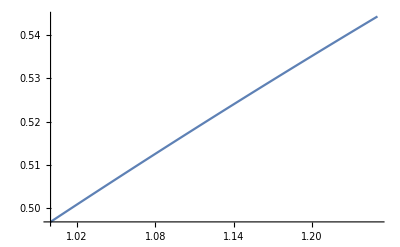

```mathematica
n=80
δ=0.8
α=2
n1=δ/α*n+1
n2 =δ/α*n-1
Plot[(n1-n2)/(n*(E01-E02)),{β, 1, 1.25}]
```